```mathematica
Class D
```

```mathematica
General 4band Hamiltonian
```

4 band General Hamiltonian

```mathematica
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
one={{1,0},{0,1}};

vx=KroneckerProduct[sx,sy];
vy=KroneckerProduct[sy,one];
vz=KroneckerProduct[sz,sy];

wx=KroneckerProduct[sy,sx];
wy=KroneckerProduct[one,sy];
wz=KroneckerProduct[sy,sz];

BeginPackage["Pfaffian`"];
Pf::usage="Pf[A] gives the pfaffian of the skew symmetric A.";
Begin["`Private`"];
Pf[A_]:=Switch[Length[A],0,1,_?OddQ,0,_?EvenQ,xPf[A,1]];
xPf[A_,p0_]:=Module[{A0,n,pivot,sign=1,A1,p1},n=Length[A]/2;
If[n≠1,A0=A;
pivot=First[Ordering[Normal[Abs[A0[[2 n-1,All]]]],-1]];
If[pivot≠2 n,A0[[{pivot,2 n},All]]=A0[[{2 n,pivot},All]];
A0[[All,{pivot,2 n}]]=A0[[All,{2 n,pivot}]];
sign=-1;];
p1=A0[[2 n-1,2 n]];
A1=p1 A0[[1;;2 n-2,1;;2 n-2]];
A1+=(#-Transpose[#])&@Outer[Times,A0[[1;;2 n-2,2 n]],A0[[1;;2 n-2,2 n-1]]];
A1/=p0;
sign xPf[A1,p1],A[[1,2]]]];
End[];
EndPackage[];

HclassD2=ax*vx+ay*vy+az*vz+bx*wx+by*wy+bz*wz;

FullSimplify[I^4*Pf[I*HclassD2]^2]
FullSimplify[Det[HclassD2]]

HclassD1={{0,a*I},{-a*I,0}};
FullSimplify[I^2*Pf[I*HclassD1]^2]
FullSimplify[Det[HclassD1]]
```

(ax^2+ay^2+az^2-bx^2-by^2-bz^2)^2

(ax^2+ay^2+az^2-bx^2-by^2-bz^2)^2

-a^2

-a^2

```mathematica
Construct SrPtAs TB model
```

Construct model SrPtAs TB

```mathematica
ClearAll["Global`*"];
Needs["VectorAnalysis`"]
$Assumptions={kx∈ Reals,ky∈ Reals,kz∈ Reals,t0∈ Reals,tz∈ Reals,tzp∈ Reals,aso∈ Reals,mu∈ Reals,p∈ Reals,d∈ Reals};

one={{1,0},{0,1}};
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};

k={kx,ky,kz};
r={x,y,z};

t[3]={1,0,0};
t[1]={-1/2,-Sqrt[3]/2,0};
t[2]={-1/2,+Sqrt[3]/2,0};

T[1]=t[3]-t[2];
T[2]=t[1]-t[3];
T[3]=t[2]-t[1];

omega[n_]:=Exp[2*Pi*I*(n)/3];

S0cost[kx_,ky_,kz_]:=Sum[Cos[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];
S0sint[kx_,ky_,kz_]:=Sum[Sin[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];
S0cosT[kx_,ky_,kz_]:=Sum[Cos[DotProduct[{kx,ky,kz},T[n]]],{n,1,3}];
S0sinT[kx_,ky_,kz_]:=Sum[Sin[DotProduct[{kx,ky,kz},T[n]]],{n,1,3}];
S1cosT[kx_,ky_,kz_]:=Sum[omega[n]*Cos[DotProduct[{kx,ky,kz},T[n]]],{n,1,3}];

H1[kx_,ky_,kz_,t0_,tzp_]:=(t0*S0cosT[kx,ky,kz]+tzp*Cos[2kz])*KroneckerProduct[one,one];

H2[kx_,ky_,kz_,tz_]:=tz*Cos[kz]*(S0cost[kx,ky,kz]*KroneckerProduct[one,sx]+S0sint[kx,ky,kz]*KroneckerProduct[one,sy]);

H3[kx_,ky_,kz_,aso_]:=aso*S0sinT[kx,ky,kz]*KroneckerProduct[sz,sz];

Hmu[kx_,ky_,kz_,mu_]:=-mu*KroneckerProduct[one,one];

Delta[kx_,ky_,kz_,p_,d_]:=p*Sin[2*kz]*KroneckerProduct[(sx-I*sy).(I*sy),sz]+d*S1cosT[kx,ky,kz]*KroneckerProduct[I*sy,one];

H[kx_,ky_,kz_,t0_,tz_,tzp_,aso_,mu_]:=H1[kx,ky,kz,t0,tzp]+H2[kx,ky,kz,tz]+H3[kx,ky,kz,aso]+Hmu[kx,ky,kz,mu];

HBdG[kx_,ky_,kz_,t0_,tz_,tzp_,aso_,mu_,p_,d_]:=ArrayFlatten[{
{H[kx,ky,kz,t0,tz,tzp,aso,mu],Delta[kx,ky,kz,p,d]},
{-Conjugate[Delta[-kx,-ky,-kz,p,d]],-Transpose[H[-kx,-ky,-kz,t0,tz,tzp,aso,mu]]}
}];
```

```mathematica
TB model Fermi surface
```

Fermi model surface TB

```mathematica
t0=1;
tz=-1;
tzp=1;
aso=-1;
mu=-3.5;

FullSimplify[Eigenvalues[H[kx,ky,kz,t0,tz,tzp,aso,mu]]];
```

```mathematica
plot=ContourPlot3D[{3.5+1. Cos[√3 ky]+1. Cos[(3 kx)/2-(√3 ky)/2]+1. Cos[1/2 (3 kx+√3 ky)]+1. Cos[2 kz]-0.25 √(48.+Cos[3 kx] (16.-16. Cos[√3 ky])+32. Cos[(3 kx)/2] Cos[(3 √3 ky)/2]-8. Cos[2 √3 ky]+(24.+32. Cos[(3 kx)/2] Cos[(√3 ky)/2]+16. Cos[√3 ky]) Cos[2 kz]),3.5+1. Cos[√3 ky]+1. Cos[(3 kx)/2-(√3 ky)/2]+1. Cos[1/2 (3 kx+√3 ky)]+1. Cos[2 kz]-0.25 √(48.+Cos[3 kx] (16.-16. Cos[√3 ky])+32. Cos[(3 kx)/2] Cos[(3 √3 ky)/2]-8. Cos[2 √3 ky]+(24.+32. Cos[(3 kx)/2] Cos[(√3 ky)/2]+16. Cos[√3 ky]) Cos[2 kz]),3.5+1. Cos[√3 ky]+1. Cos[(3 kx)/2-(√3 ky)/2]+1. Cos[1/2 (3 kx+√3 ky)]+1. Cos[2 kz]+0.25 √(48.+Cos[3 kx] (16.-16. Cos[√3 ky])+32. Cos[(3 kx)/2] Cos[(3 √3 ky)/2]-8. Cos[2 √3 ky]+(24.+32. Cos[(3 kx)/2] Cos[(√3 ky)/2]+16. Cos[√3 ky]) Cos[2 kz]),3.5+1. Cos[√3 ky]+1. Cos[(3 kx)/2-(√3 ky)/2]+1. Cos[1/2 (3 kx+√3 ky)]+1. Cos[2 kz]+0.25 √(48.+Cos[3 kx] (16.-16. Cos[√3 ky])+32. Cos[(3 kx)/2] Cos[(3 √3 ky)/2]-8. Cos[2 √3 ky]+(24.+32. Cos[(3 kx)/2] Cos[(√3 ky)/2]+16. Cos[√3 ky]) Cos[2 kz])}==0,(*{kx,-2*Pi/3,+2Pi/3},{ky,-4*Pi/3/Sqrt[3],4*Pi/3/Sqrt[3]},{kz,-Pi/2,Pi/2},*)
{kx,-Pi,Pi},{ky,-Pi,Pi},{kz,-Pi/2,Pi/2},
PlotPoints->15,RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False,
Mesh->None,
ContourStyle->Directive[FaceForm[LightBlue,Blue],Specularity[White,30]]];

(* ContourPlot3D[Evaluate[torus[{3,1},{x,y,z}]],{x,-5,5},{y,-5,5},{z,-5,5},Mesh->None,ContourStyle->Directive[Orange,Specularity[White,20]],PlotPoints->25,PlotRange->Automatic,BoxRatios->Automatic]*)



Lv1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-Pi/2},{0,4*Pi/3/Sqrt[3],+Pi/2}}]];
Lv2=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-Pi/2},{0,-4*Pi/3/Sqrt[3],+Pi/2}}]];
Lv3=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-Pi/2},{2*Pi/3,2*Pi/3/Sqrt[3],+Pi/2}}]];
Lv4=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-Pi/2},{2*Pi/3,-2*Pi/3/Sqrt[3],+Pi/2}}]];
Lv5=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-Pi/2},{-2*Pi/3,2*Pi/3/Sqrt[3],+Pi/2}}]];
Lv6=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-Pi/2},{-2*Pi/3,-2*Pi/3/Sqrt[3],+Pi/2}}]];

Ltop1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],+Pi/2},{2*Pi/3,2*Pi/3/Sqrt[3],+Pi/2}}]];
Ltop2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],+Pi/2},{2*Pi/3,-2*Pi/3/Sqrt[3],+Pi/2}}]];
Ltop3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],+Pi/2},{0,-4*Pi/3/Sqrt[3],+Pi/2}}]];
Ltop4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],+Pi/2},{-2*Pi/3,-2*Pi/3/Sqrt[3],+Pi/2}}]];
Ltop5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],+Pi/2},{-2*Pi/3,2*Pi/3/Sqrt[3],+Pi/2}}]];
Ltop6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],+Pi/2},{0,4*Pi/3/Sqrt[3],+Pi/2}}]];

Lbot1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-Pi/2},{2*Pi/3,2*Pi/3/Sqrt[3],-Pi/2}}]];
Lbot2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-Pi/2},{2*Pi/3,-2*Pi/3/Sqrt[3],-Pi/2}}]];
Lbot3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-Pi/2},{0,-4*Pi/3/Sqrt[3],-Pi/2}}]];
Lbot4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-Pi/2},{-2*Pi/3,-2*Pi/3/Sqrt[3],-Pi/2}}]];
Lbot5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-Pi/2},{-2*Pi/3,2*Pi/3/Sqrt[3],-Pi/2}}]];
Lbot6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-Pi/2},{0,4*Pi/3/Sqrt[3],-Pi/2}}]];

Rasterize[Show[{plot,Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,Ltop1,Ltop2,Ltop3,Ltop4,Ltop5,Ltop6,Lbot1,Lbot2,Lbot3,Lbot4,Lbot5,Lbot6},ViewPoint->{2,2,1}],RasterSize->1000]
```

-Graphics-

```mathematica
Pfaffian of rotated TB model
```

model of Pfaffian rotated TB

```mathematica
Clear[kx,ky,kz]

BeginPackage["Pfaffian`"];
Pf::usage="Pf[A] gives the pfaffian of the skew symmetric A.";
Begin["`Private`"];
Pf[A_]:=Switch[Length[A],0,1,_?OddQ,0,_?EvenQ,xPf[A,1]];
xPf[A_,p0_]:=Module[{A0,n,pivot,sign=1,A1,p1},n=Length[A]/2;
If[n≠1,A0=A;
pivot=First[Ordering[Normal[Abs[A0[[2 n-1,All]]]],-1]];
If[pivot≠2 n,A0[[{pivot,2 n},All]]=A0[[{2 n,pivot},All]];
A0[[All,{pivot,2 n}]]=A0[[All,{2 n,pivot}]];
sign=-1;];
p1=A0[[2 n-1,2 n]];
A1=p1 A0[[1;;2 n-2,1;;2 n-2]];
A1+=(#-Transpose[#])&@Outer[Times,A0[[1;;2 n-2,2 n]],A0[[1;;2 n-2,2 n-1]]];
A1/=p0;
sign xPf[A1,p1],A[[1,2]]]];
End[];
EndPackage[];

U={{1,-I},{1,I}}/Sqrt[2];
bigU=KroneckerProduct[ConjugateTranspose[U],one,ConjugateTranspose[U]];

HclassD2[kx_,ky_,kz_,t0_,tz_,tzp_,aso_,mu_,p_,d_]:=FullSimplify[bigU.HBdG[kx,ky,kz,t0,tz,tzp,aso,mu,p,d].ConjugateTranspose[bigU]];
(* FullSimplify[HclassD2[kx,ky,kz,t0,tz,tzp,aso,mu,p,d]+Transpose[HclassD2[kx,ky,kz,t0,tz,tzp,aso,mu,p,d]]]; *)

t0=1;
tz=-1;
tzp=1;
aso=-1;
mu=-3.5;
p=0.2;
d=0.2;

(*Pf[HclassD2[kx,ky,kz,t0,tz,tzp,aso,mu,p,d]]*)

Pfaf[kx_,ky_,kz_]:=(-(((1.+0. ⅈ) (((0.+0. ⅈ)+((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((0.-0.2 ⅈ) Cos[√3 ky]+(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)-(1.+0. ⅈ) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))-((0.+0. ⅈ)-(0.+1. ⅈ) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz])) ((0.+0. ⅈ)+((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])-(0.+1. ⅈ) ((0.+2. ⅈ) Cos[kx/2]-(0.+2. ⅈ) Cos[(√3 ky)/2]) Cos[kz] Sin[kx/2] (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)+(0.+1. ⅈ) ((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz])) ((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))) (-((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((0.-0.2 ⅈ) Cos[√3 ky]+(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)+(1.+0. ⅈ) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)-(0.+1. ⅈ) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz])) ((0.+0. ⅈ)-((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])-(0.+1. ⅈ) ((0.+2. ⅈ) Cos[kx/2]-(0.+2. ⅈ) Cos[(√3 ky)/2]) Cos[kz] Sin[kx/2] (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)+(0.+1. ⅈ) ((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz])) ((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))))/(Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])^2)+((1.+0. ⅈ) (-((0.+0. ⅈ)-(0.+1. ⅈ) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz])) ((0.+0. ⅈ)+(1.+0. ⅈ) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)+((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((0.-0.2 ⅈ) Cos[√3 ky]+(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)-((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])-(0.+1. ⅈ) ((0.+2. ⅈ) Cos[kx/2]-(0.+2. ⅈ) Cos[(√3 ky)/2]) Cos[kz] Sin[kx/2] (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)-((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((3.469446951953614*^-17+0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))) (((0.+0. ⅈ)-(0.+1. ⅈ) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz])) ((0.+0. ⅈ)-(1.+0. ⅈ) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))-((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((0.-0.2 ⅈ) Cos[√3 ky]+(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)+((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])-(0.+1. ⅈ) ((0.+2. ⅈ) Cos[kx/2]-(0.+2. ⅈ) Cos[(√3 ky)/2]) Cos[kz] Sin[kx/2] (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)+((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((3.469446951953614*^-17+0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))))/(Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])^2-((1.+0. ⅈ) (-((0.+0. ⅈ)+(1.+0. ⅈ) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)-(1.+0. ⅈ) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)-((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])-(0.+1. ⅈ) ((0.+2. ⅈ) Cos[kx/2]-(0.+2. ⅈ) Cos[(√3 ky)/2]) Cos[kz] Sin[kx/2] (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)+((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])-(0.+1. ⅈ) ((0.+2. ⅈ) Cos[kx/2]-(0.+2. ⅈ) Cos[(√3 ky)/2]) Cos[kz] Sin[kx/2] (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)-((0.+0.2 ⅈ) Cos[√3 ky]-(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]-(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))) (((0.+0. ⅈ)-(0.+1. ⅈ) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz])) ((0.+0. ⅈ)-(0.+1. ⅈ) ((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz]))-((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((0.-0.2 ⅈ) Cos[√3 ky]+(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((0.+0. ⅈ)+((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)]) Cos[kz] ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])-(0.+1. ⅈ) ((0.-0.2 ⅈ) Cos[√3 ky]+(1.3877787807814457*^-17+0.09999999999999998 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(0.+0.1 ⅈ) Cos[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]))+((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])) ((-1.+0. ⅈ) (-3.5-1. Cos[√3 ky]-1. Cos[(3 kx)/2-(√3 ky)/2]-1. Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]-1. Cos[2 kz]) (3.5+Cos[√3 ky]+Cos[(3 kx)/2-(√3 ky)/2]+Cos[1/2 (3 kx+√3 ky)]+(Cos[kx]+2 Cos[kx/2] Cos[(√3 ky)/2]) Cos[kz]+Cos[2 kz])+Cos[kz]^2 ((0.-2. ⅈ) Cos[(√3 ky)/2] Sin[kx/2]+(0.+1. ⅈ) Sin[kx])^2-(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]+0.8 Cos[kz] Sin[kz]))))/(Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz])^2)/((0.+0. ⅈ)-((-3.469446951953614*^-17-0.17320508075688773 ⅈ) Cos[(3 kx)/2-(√3 ky)/2]+(2.7755575615628914*^-17+0.1732050807568877 ⅈ) Cos[1/2 (3 kx+√3 ky)])^2+(1.+0. ⅈ) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]) (Sin[√3 ky]+Sin[(3 kx)/2-(√3 ky)/2]-1. Sin[1/2 (3 kx+√3 ky)]-0.8 Cos[kz] Sin[kz]));
```

```mathematica
Plot nodal surface of TB model
```

model nodal of Plot surface TB

```mathematica
(*kxMin=-0.23;
kxMax=0.23;
kyMin=-4*Pi/3/Sqrt[3]-0.23;
kyMax=-4*Pi/3/Sqrt[3]+0.23;
kzMin=0.75;
kzMax=0.79;*)

kxMin=-0.03;
kxMax=0.03;
kyMin=-4*Pi/3/Sqrt[3]-0.03;
kyMax=-4*Pi/3/Sqrt[3]+0.03;
kzMin=0.46;
kzMax=0.48;

pts=80;
surf=ConstantArray[0,{(pts+1)^3,4}];
surf2=ConstantArray[0,{pts+1,pts+1,pts+1}];

For[a=1,a<pts+2,a++,
kx=kxMin+(a-1)*(kxMax-kxMin)/pts;
For[b=1,b<pts+2,b++,
ky=kyMin+(b-1)*(kyMax-kyMin)/pts;
For[c=1,c<pts+2,c++,
kz=kzMin+(c-1)*(kzMax-kzMin)/pts;
pf=Re[Pfaf[kx,ky,kz]];

surf2[[a,b,c]]=pf;

];
];
Print[a];
];

surf3=ConstantArray[0,{pts+1,pts+1,pts+1}];
For[a=1,a<pts+2,a++,
For[b=1,b<pts+2,b++,
For[c=1,c<pts+2,c++,
surf3[[a,b,c]]=surf2[[b,c,a]];
];
];
];

lplot=ListContourPlot3D[surf3,Contours->{0},BoxStyle-> Thick,Ticks->{
{{(-2.4-kyMin)*pts/(kyMax-kyMin),-2.4},{(-2.42-kyMin)*pts/(kyMax-kyMin),-2.42},{(-2.44-kyMin)*pts/(kyMax-kyMin),-2.44}},
{{(-0.03-kxMin)*pts/(kxMax-kxMin),-0.03},{(-0.02-kxMin)*pts/(kxMax-kxMin),-0.02},{(-0.01-kxMin)*pts/(kxMax-kxMin),-0.01},{(0-kxMin)*pts/(kxMax-kxMin),0},{(0.01-kxMin)*pts/(kxMax-kxMin),0.01},{(0.02-kxMin)*pts/(kxMax-kxMin),0.02},{(0.03-kxMin)*pts/(kxMax-kxMin),0.03}},{{(0.76-kzMin)*pts/(kzMax-kzMin),0.76},{(0.761-kzMin)*pts/(kzMax-kzMin),0.761},{(0.46-kzMin)*pts/(kzMax-kzMin),0.46},{(0.465-kzMin)*pts/(kzMax-kzMin),0.465},{(0.47-kzMin)*pts/(kzMax-kzMin),0.47},{(0.475-kzMin)*pts/(kzMax-kzMin),0.475},{(0.48-kzMin)*pts/(kzMax-kzMin),0.48}}
},TicksStyle->Directive[Thick, 18],(*PlotTheme->"ThickSurface",*)AxesLabel->{Style["\!\(\*SubscriptBox[\(k\), \(y\)]\)a",Italic],Style["\!\(\*SubscriptBox[\(k\), \(x\)]\)a",Italic],Style["\!\(\*SubscriptBox[\(k\), \(z\)]\)c",Italic]},AxesStyle->Directive[Thick, 20],LabelStyle->Directive[Thick, 20],Mesh->None,
ContourStyle->Directive[FaceForm[Blue,LightBlue],Specularity[White,30]]];

Rasterize[Show[lplot,ViewPoint->{-12/3,-5/3,1.4}],RasterSize->1000]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

-Graphics-

```mathematica
Plot Sign[Pf[H]] for a cut through nodal surface
```

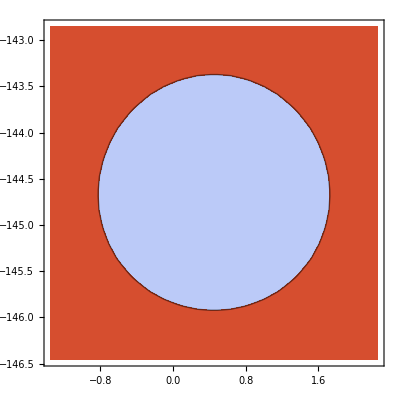

```mathematica
kxMin=-0.03;
kxMax=0.03;
kyMin=-4*Pi/3/Sqrt[3]-0.03;
kyMax=-4*Pi/3/Sqrt[3]+0.03;

kz=0.47;

pts=20;
surf=ConstantArray[0,{(pts+1)^2,3}];

For[b=1,b<pts+2,b++,
kx=kxMin+(b-1)*(kxMax-kxMin)/pts;
For[c=1,c<pts+2,c++,
ky=kyMin+(c-1)*(kyMax-kyMin)/pts;
pf=Re[Pfaf[kx,ky,kz]];

surf[[(b-1)*(pts+1)+(c-1)+1,1]]=kx;
surf[[(b-1)*(pts+1)+(c-1)+1,2]]=ky;
surf[[(b-1)*(pts+1)+(c-1)+1,3]]=pf;

]
];
shift=0.25;
mult=1.8;
ListContourPlot[mult*(shift+surf/Max[surf]),Contours->{mult*shift},MaxPlotPoints->50,ColorFunction->"TemperatureMap",AxesLabel->None,Ticks->None,FrameTicksStyle->Directive[0],PlotRange->Full,ColorFunctionScaling->False]
```

```mathematica
Plot Berry curvature on a sphere surrounding nodal surface
```

```mathematica
(* Check the Chern number *)

t0=1;
tz=-1;
tzp=1;
aso=-1;
mu=-3.5;
p=0.2;
d=0.2;

cx=0;
cy=-4*Pi/3/Sqrt[3];
cz=0.47;
R=0.1;

pts=200;

states=ConstantArray[0,{pts+1,pts,4}];

For[i=1,i<pts+2,i++,
For[j=1,j<pts+1,j++,

theta=(i-1)*Pi/pts;
fi=(j-1)*2*Pi/pts;

kx=cx+R*Sin[theta]*Cos[fi];
ky=cy+R*Sin[theta]*Sin[fi];
kz=cz+R*Cos[theta];

sys=Transpose[Sort[Transpose[Eigensystem[N[HBdG[kx,ky,kz,t0,tz,tzp,aso,mu,p,d]]]]]];

For[a=1,a<4+1,a++,
states[[i,j,a]]=Normalize[sys[[2,a]]];
];
];
];

F=ConstantArray[0,{pts,pts-1}];
f=0;

toplot=ConstantArray[0,{pts,pts-1}];

For[i=1,i<pts+1,i++,
For[j=1,j<pts,j++,

theta=(i)*Pi/pts;
fi=(j)*2*Pi/pts;

dS=2*(R*Pi/pts)^2*Sin[theta];

F[[i,j]]=Sum[Arg[((Conjugate[{states[[i,j,a]]}].Transpose[{states[[i+1,j,a]]}])[[1,1]])*((Conjugate[{states[[i+1,j,a]]}].Transpose[{states[[i+1,j+1,a]]}])[[1,1]])*((Conjugate[{states[[i+1,j+1,a]]}].Transpose[{states[[i,j+1,a]]}])[[1,1]])*((Conjugate[{states[[i,j+1,a]]}].Transpose[{states[[i,j,a]]}])[[1,1]])],{a,1,4}];

toplot[[i,j]]=r*F[[i,j]]/Max[dS,dSmin];

f+=F[[i,j]];
];
];


Print[f/(2*Pi)];
(*ListDensityPlot[(1+F/Max[F])/2,PlotRange->Full,ColorFunction->"LightTemperatureMap",ColorFunctionScaling->False]
ListPlot3D[(1+F/Max[F])/2]*)

plt=ListDensityPlot[(1+toplot/Max[toplot])/2,PlotRange->{{x,0,Pi},{y,0,2 Pi}},PlotRangePadding->0,Frame->False,ColorFunction->"TemperatureMap",ColorFunctionScaling->False];

final=SphericalPlot3D[1,{u,0,Pi},{v,0,2 Pi},Mesh->None,TextureCoordinateFunction->({#5,1-#4}&),PlotStyle->Directive[Texture[plt]],Lighting->"Neutral",SphericalRegion->True,RotationAction->"Clip",Boxed->False,Axes->False];

Rasterize[Show[final,ViewPoint->{-12/3,-5/3,1.4}],RasterSize->1000]
```

1.98998

```mathematica
Class BDI
```

```mathematica
General 4 band Hamiltonian
```

```mathematica
ClearAll["Global`*"];
$Assumptions={p1∈ Reals,p2∈ Reals,r1∈ Reals,r2∈ Reals,p∈ Reals,fip∈ Reals,r∈ Reals,fir∈ Reals};

sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
one={{1,0},{0,1}};

vx=KroneckerProduct[sx,one];
vy=KroneckerProduct[-sy,sy];
wx=KroneckerProduct[sx,sz];
wy=KroneckerProduct[-sx,sx];

H[p_,fip_,r_,fir_]:=p*Cos[fip]*vx+p*Sin[fip]*vy+r*Cos[fir]*wx+r*Sin[fir]*wy;

(* H[p1,p2,r1,r2]//MatrixForm *)

eigsys=FullSimplify[Eigensystem[FullSimplify[H[0,0,r,fir]]]];

(* p<r GIVES here 1+2 negative and 3+4 positive energy! *)

v1=FullSimplify[{Normalize[eigsys[[2,1]]]}];
v2=FullSimplify[{Normalize[eigsys[[2,2]]]}];
v3=FullSimplify[{Normalize[eigsys[[2,3]]]}];
v4=FullSimplify[{Normalize[eigsys[[2,4]]]}];

Q=FullSimplify[-Transpose[v2].Conjugate[v2]+Transpose[v4].Conjugate[v4]-Transpose[v1].Conjugate[v1]+Transpose[v3].Conjugate[v3]]//MatrixForm
```

(0 | 0 | Cos[fir] | -Sin[fir]
0 | 0 | -Sin[fir] | -Cos[fir]
Cos[fir] | -Sin[fir] | 0 | 0
-Sin[fir] | -Cos[fir] | 0 | 0)

```mathematica
Construct dimerized AAA graphite TB model
```

```mathematica
ClearAll["Global`*"];
Needs["VectorAnalysis`"]
$Assumptions={kx∈ Reals,ky∈ Reals,kz∈ Reals,t1∈ Reals,t2∈ Reals,t3∈ Reals,r∈ Reals};

one={{1,0},{0,1}};
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};

sPlus=(sx+I*sy)/2;
sMinus=(sx-I*sy)/2;

k={kx,ky,kz};

t[3]={1,0,0};
t[1]={-1/2,-Sqrt[3]/2,0};
t[2]={-1/2,+Sqrt[3]/2,0};

S0cost[kx_,ky_,kz_]:=Sum[Cos[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];
S0sint[kx_,ky_,kz_]:=Sum[Sin[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];

H1[kx_,ky_,kz_,t1_]:=t1*(S0cost[kx,ky,kz]*KroneckerProduct[one,sx]-S0sint[kx,ky,kz]*KroneckerProduct[one,sy]);
H2[kz_,t2_,t3_,r_]:=((t2*Exp[I*kz]+t3*Exp[-I*r*kz])*KroneckerProduct[sPlus,one]+(t2*Exp[-I*kz]+t3*Exp[I*r*kz])*KroneckerProduct[sMinus,one]);
HBDI[kx_,ky_,kz_,t1_,t2_,t3_,r_]:=H1[kx,ky,kz,t1]+H2[kz,t2,t3,r];
```

```mathematica
TB model Fermi surface
```

```mathematica
t1=1;
t2=1/2;
t3=1/10;
r=2;

 (*FullSimplify[Eigenvalues[HBDI[kx,ky,kz,t1,t2,t3,r]]] *)

BZheight=Pi/3;

plot=ContourPlot3D[(137+100 Cos[√3 ky]+100 Cos[(3 kx)/2-(√3 ky)/2]+100 Cos[1/2 (3 kx+√3 ky)]-5 Cos[3 kz])/50==0,
{kx,-Pi,Pi},{ky,-Pi,Pi},{kz,-BZheight,BZheight},
PlotPoints->30,RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False,
Mesh->None,
ContourStyle->Directive[FaceForm[LightBlue,Blue],Specularity[White,30]]];

Lv1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-BZheight},{0,4*Pi/3/Sqrt[3],+BZheight}}]];
Lv2=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-BZheight},{0,-4*Pi/3/Sqrt[3],+BZheight}}]];
Lv3=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Lv4=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];
Lv5=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Lv6=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];

Ltop1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],+BZheight},{2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],+BZheight},{2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight},{0,-4*Pi/3/Sqrt[3],+BZheight}}]];
Ltop4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],+BZheight},{-2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight},{-2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],+BZheight},{0,4*Pi/3/Sqrt[3],+BZheight}}]];

Lbot1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{0,-4*Pi/3/Sqrt[3],-BZheight}}]];
Lbot4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{0,4*Pi/3/Sqrt[3],-BZheight}}]];

Circle3D[centre_: {0,0,0},radius_: 1,normal_: {0,0,1},angle_: {0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle≥2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]];

outer= Graphics3D[{RGBColor[0,0.6,0],Thickness[0.007],Circle3D[{0,4*Pi/3/Sqrt[3],0},0.6 ]}];
inner= Graphics3D[{Red,Thickness[0.007],Circle3D[{0,4*Pi/3/Sqrt[3],0},0.3 ]}];

Rasterize[Show[{plot,Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,Ltop1,Ltop2,Ltop3,Ltop4,Ltop5,Ltop6,Lbot1,Lbot2,Lbot3,Lbot4,Lbot5,Lbot6,outer,inner},ViewPoint->{2,2,1}],RasterSize->1000]
```

-Graphics-

```mathematica
SO(n) winding invariant for horizontla loops
```

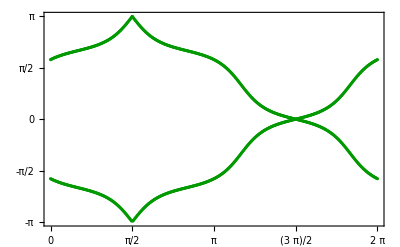

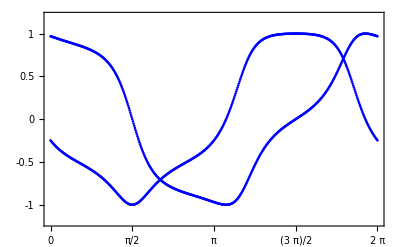

```mathematica
t1=1;
t2=0.5;
t3=0.1;
r=2;

(* the following are equivalent *)
U={{1/(√2),0,0,1/(√2)},{ⅈ/(√2),0,0,-ⅈ/(√2)},{0,1/(√2),1/(√2),0},{0,-ⅈ/(√2),ⅈ/(√2),0}};

(* 
the S^1 loop is centered on K point 
small R like 0.1 is a contractible loop inside the cylinder
large R like 1 is a non-contractible loop oustide the cylinder
*)
R=1;
kz=0;

pts=500;

args=ConstantArray[0,{pts+1,2}];
sin=ConstantArray[0,{pts+1}];
cos=ConstantArray[0,{pts+1}];

For[i=1,i<pts+2,i++,
fi=2*Pi*(i-1)/pts;

kx=R*Cos[fi];
ky=4*Pi/3/Sqrt[3]+R*Sin[fi];

M=N[U.HBDI[kx,ky,kz,t1,t2,t3,r].ConjugateTranspose[U]];

sys=Transpose[Sort[Transpose[Eigensystem[N[M]]]]];
u1={Normalize[sys[[2,1]]]};
u2={Normalize[sys[[2,2]]]};
u3={Normalize[sys[[2,3]]]};
u4={Normalize[sys[[2,4]]]};

(* The projected "flat-band" Hamiltonian *)
Q=-Transpose[u1].Conjugate[u1]-Transpose[u2].Conjugate[u2]+Transpose[u3].Conjugate[u3]+Transpose[u4].Conjugate[u4];

(* off-diag block of the flat-band Hamiltonian from SO(2) *)
q={
{Q[[1,3]],Q[[1,4]]},
{Q[[2,3]],Q[[2,4]]}
};
If[Re[Det[q]]<0,
q={{1,0},{0,-1}}.q;
];

eigs=Sort[Im[Log[Eigenvalues[q]]]];
args[[i,1]]=eigs[[1]];
args[[i,2]]=eigs[[2]];
cos[[i]]=q[[1,1]];
sin[[i]]=q[[2,1]];
];

ListPlot[Transpose[args],
PlotRange->{{1,1+pts},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/2},{1+pts/2,Pi},{1+3*pts/4,3Pi/2},{1+pts,2*Pi}},
{0,Pi/2,Pi,-Pi/2,-Pi}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->RGBColor[0,0.6,0],
(*PlotStyle->Red,*)
FrameStyle->Thick
]

ListPlot[{Re[cos],Re[sin]},
PlotRange->{{1,1+pts},{-1.2,1.2}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/2},{1+pts/2,Pi},{1+3*pts/4,3Pi/2},{1+pts,2*Pi}},
{0,0.5,-0.5,1,-1}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]

(* 
Observe non-trivial winding for large R, i.e. a path 
looping around the cylinder! On the other hand, the winding is 
trivial for small R!
*)
```

```mathematica
Plot Sign[Det[H]] for a cut through nodal surface
```

```mathematica
t1=1;
t2=0.5;
t3=0.1;
r=2;

kxMin=-Pi;
kxMax=Pi;
kyMin=-Pi;
kyMax=Pi;

kz=Pi/3;

pts=300;
surf=ConstantArray[0,{(pts+1)^2,3}];

For[b=1,b<pts+2,b++,
kx=kxMin+(b-1)*(kxMax-kxMin)/pts;
For[c=1,c<pts+2,c++,
ky=kyMin+(c-1)*(kyMax-kyMin)/pts;

M=N[U.HBDI[kx,ky,kz,t1,t2,t3,r].ConjugateTranspose[U]];

sys=Transpose[Sort[Transpose[Eigensystem[N[M]]]]];
u1={Normalize[sys[[2,1]]]};
u2={Normalize[sys[[2,2]]]};
u3={Normalize[sys[[2,3]]]};
u4={Normalize[sys[[2,4]]]};

(* The projected "flat-band" Hamiltonian *)
Q=-Transpose[u1].Conjugate[u1]-Transpose[u2].Conjugate[u2]+Transpose[u3].Conjugate[u3]+Transpose[u4].Conjugate[u4];

(* off-diag block of the flat-band Hamiltonian from SO(2) *)
q={
{Q[[1,3]],Q[[1,4]]},
{Q[[2,3]],Q[[2,4]]}
};

det=Det[q];

surf[[(b-1)*(pts+1)+(c-1)+1,1]]=kx;
surf[[(b-1)*(pts+1)+(c-1)+1,2]]=ky;
surf[[(b-1)*(pts+1)+(c-1)+1,3]]=Sign[det];

]
];
shift=0.72;
mult=0.9;
ListContourPlot[mult*(shift+surf/Max[surf]),Contours->{mult*shift},MaxPlotPoints->pts,ColorFunction->"TemperatureMap",AxesLabel->None,Ticks->None,FrameTicksStyle->Directive[0],PlotRange->Full,ColorFunctionScaling->False]
```

-Graphics-

```mathematica
Class CI
```

```mathematica
4band examples with (non)-trivial pi2-charge
```

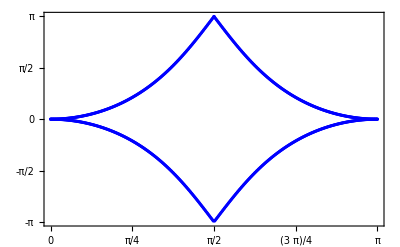

```mathematica
ClearAll["Global`*"];
$Assumptions={ax∈ Reals,ay∈ Reals,az∈ Reals,bx∈ Reals,by∈ Reals,bz∈ Reals,kx∈ Reals,ky∈ Reals,kz∈ Reals,m∈ Reals,m2∈ Reals};

sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
one={{1,0},{0,1}};

vx=KroneckerProduct[sz,sz];
vy=KroneckerProduct[-sz,sx];
vz=KroneckerProduct[sx,one];

wx=KroneckerProduct[-sx,sz];
wy=KroneckerProduct[sx,sx];
wz=KroneckerProduct[sz,one];

Hnontriv[kx_,ky_,kz_]:=kx*vx+ky*vy+kz*vz+wz;
Htriv[kx_,ky_,kz_]:=Sqrt[kx^2+ky^2]*vz+kz*vz+wz;

R=2;
pts=500; (* 500 *)

shift=0.001;

argsu=ConstantArray[0,{pts+1,2}];
argsv=ConstantArray[0,{pts+1,2}];

For[b=1,b<pts+1,b++,
theta=Pi*(b-1)/pts;
fi=0;
kx=R*Sin[theta]*Cos[fi]+shift;
ky=R*Sin[theta]*Sin[fi];
kz=R*Cos[theta];

proju={{1,0},{0,1}};
projv={{1,0},{0,1}};

eigs=Transpose[Sort[Transpose[Eigensystem[N[Hnontriv[kx,ky,kz]]]]]];
uS1=Normalize[eigs[[2,1]]];
uS2=Normalize[eigs[[2,2]]];
vS1=Normalize[eigs[[2,3]]];
vS2=Normalize[eigs[[2,4]]];

u1old=uS1;
u2old=uS2;
v1old=vS1;
v2old=vS2;

For[a=1,a<pts+1,a++,
fi=2*a*Pi/pts;
kx=R*Sin[theta]*Cos[fi]+shift;
ky=R*Sin[theta]*Sin[fi];
kz=R*Cos[theta];

eigs=Transpose[Sort[Transpose[Eigensystem[N[Hnontriv[kx,ky,kz]]]]]];
u1=Normalize[eigs[[2,1]]];
u2=Normalize[eigs[[2,2]]];
v1=Normalize[eigs[[2,3]]];
v2=Normalize[eigs[[2,4]]];
(*
Mu={{u1.u1old,u1.u2old},{u2.u1old,u2.u2old}};
Mv={{v1.v1old,v1.v2old},{v2.v1old,v2.v2old}};
*)

Mu={{u1.Conjugate[u1old],u1.Conjugate[u2old]},{u2.Conjugate[u1old],u2.Conjugate[u2old]}};
Mv={{v1.Conjugate[v1old],v1.Conjugate[v2old]},{v2.Conjugate[v1old],v2.Conjugate[v2old]}};


proju=Mu.proju;
projv=Mv.projv;

u1old=u1;
u2old=u2;
v1old=v1;
v2old=v2;
];

(*
proju={{uS1.u1old,uS1.u2old},{uS2.u1old,uS2.u2old}}.proju;
projv={{vS1.v1old,vS1.v2old},{vS2.v1old,vS2.v2old}}.projv;
*)

proju={{uS1.Conjugate[u1old],uS1.Conjugate[u2old]},{uS2.Conjugate[u1old],uS2.Conjugate[u2old]}}.proju;
projv={{vS1.Conjugate[v1old],vS1.Conjugate[v2old]},{vS2.Conjugate[v1old],vS2.Conjugate[v2old]}}.projv;


If[Re[Det[proju]]<0,
proju=sz.proju;
];
If[Re[Det[projv]]<0,
projv=sz.projv;
];

argsu[[b]]=Arg[Eigenvalues[proju]];
argsv[[b]]=Arg[Eigenvalues[projv]];
];

ListPlot[Transpose[argsu],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]
```

```mathematica
Construct TB model on AAA stacked graphite
```

```mathematica
ClearAll["Global`*"];
Needs["VectorAnalysis`"]
$Assumptions={kx∈ Reals,ky∈ Reals,kz∈ Reals,t1∈ Reals,t2∈ Reals,psi∈ Reals,delta∈ Reals};

one={{1,0},{0,1}};
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};

k={kx,ky,kz};

t[3]={1,0,0};
t[1]={-1/2,-Sqrt[3]/2,0};
t[2]={-1/2,+Sqrt[3]/2,0};

S0cost[kx_,ky_,kz_]:=Sum[Cos[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];
S0sint[kx_,ky_,kz_]:=Sum[Sin[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];

H1[kx_,ky_,kz_,t1_]:=t1*(S0cost[kx,ky,kz]*sx-S0sint[kx,ky,kz]*sy);
H2[kz_,t2_]:=2t2*Cos[kz]*one;

HCI[kx_,ky_,kz_,t1_,t2_]:=H1[kx,ky,kz,t1]+H2[kz,t2];
Gap[kz_,psi_,delta_]:=psi*(delta+Cos[kz])*one;

Hred[kx_,ky_,kz_,t1_,t2_,psi_,delta_]:=ArrayFlatten[{
{HCI[kx,ky,kz,t1,t2],Gap[kz,psi,delta]},
{Gap[kz,psi,delta],-HCI[kx,ky,kz,t1,t2]}
}];
```

```mathematica
TB model (non-SC)  Fermi surface
```

```mathematica
t1=1;
t2=2/5;

(*FullSimplify[Eigenvalues[HCI[kx,ky,kz,t1,t2]]]*)

BZheight=Pi;

plot=ContourPlot3D[{-√(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+(4 Cos[kz])/5==0,√(3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+(4 Cos[kz])/5==0},
{kx,-Pi,Pi},{ky,-Pi,Pi},{kz,-BZheight,BZheight},
PlotPoints->30,RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False,
Mesh->None,
ContourStyle->{Directive[FaceForm[Red,LightRed],Specularity[White,30]],Directive[FaceForm[LightBlue,Blue],Specularity[White,30]]}];

Lv1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-BZheight},{0,4*Pi/3/Sqrt[3],+BZheight}}]];
Lv2=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-BZheight},{0,-4*Pi/3/Sqrt[3],+BZheight}}]];
Lv3=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Lv4=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];
Lv5=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Lv6=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];

Ltop1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],+BZheight},{2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],+BZheight},{2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight},{0,-4*Pi/3/Sqrt[3],+BZheight}}]];
Ltop4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],+BZheight},{-2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],+BZheight},{-2*Pi/3,2*Pi/3/Sqrt[3],+BZheight}}]];
Ltop6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],+BZheight},{0,4*Pi/3/Sqrt[3],+BZheight}}]];

Lbot1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{0,-4*Pi/3/Sqrt[3],-BZheight}}]];
Lbot4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-BZheight},{-2*Pi/3,2*Pi/3/Sqrt[3],-BZheight}}]];
Lbot6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-BZheight},{0,4*Pi/3/Sqrt[3],-BZheight}}]];

Circle3D[centre_: {0,0,0},radius_: 1,normal_: {0,0,1},angle_: {0,2 Pi}]:=Composition[Line,Map[RotationTransform[{{0,0,1},normal},centre],#]&,Map[Append[#,Last@centre]&,#]&,Append[DeleteDuplicates[Most@#],Last@#]&,Level[#,{-2}]&,MeshPrimitives[#,1]&,DiscretizeRegion,If][First@Differences@angle≥2 Pi,Circle[Most@centre,radius],Circle[Most@centre,radius,angle]];

Rasterize[Show[{plot,Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,Ltop1,Ltop2,Ltop3,Ltop4,Ltop5,Ltop6,Lbot1,Lbot2,Lbot3,Lbot4,Lbot5,Lbot6},ViewPoint->{2,2,1}],RasterSize->1000]
```

-Graphics-

```mathematica
Wilson loop eigenvalue winding
```

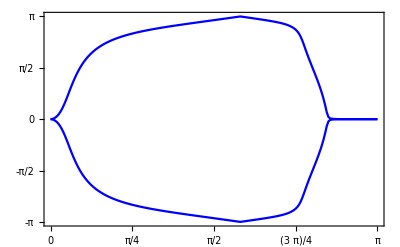

-Graphics-

```mathematica
t1=1;
t2=2/5;
psi=0.2;
delta=-Sqrt[3]/2;

pts=200;

R=Pi/3; (* Pi/3*)
xc=0;
yc=4*Pi/3/Sqrt[3];
zc= Pi/4; (* 0 or Pi/4 *)
 
argsu=ConstantArray[0,{pts+1,2}];
argsv=ConstantArray[0,{pts+1,2}];

For[b=1,b<pts+1,b++,
theta=Pi*(b-1)/pts;

fi=0;
kx=xc+R*Sin[theta]*Cos[fi];
ky=yc+R*Sin[theta]*Sin[fi];
kz=zc+R*Cos[theta];

proju={{1,0},{0,1}};
projv={{1,0},{0,1}};

eigs=Transpose[Sort[Transpose[Eigensystem[N[Hred[kx,ky,kz,t1,t2,psi,delta]]]]]];
uS1=Normalize[eigs[[2,1]]];
uS2=Normalize[eigs[[2,2]]];
vS1=Normalize[eigs[[2,3]]];
vS2=Normalize[eigs[[2,4]]];

u1old=uS1;
u2old=uS2;
v1old=vS1;
v2old=vS2;

For[a=1,a<pts+1,a++,
fi=2*a*Pi/pts;
kx=xc+R*Sin[theta]*Cos[fi];
ky=yc+R*Sin[theta]*Sin[fi];
kz=zc+R*Cos[theta];

eigs=Transpose[Sort[Transpose[Eigensystem[N[Hred[kx,ky,kz,t1,t2,psi,delta]]]]]];
u1=Normalize[eigs[[2,1]]];
u2=Normalize[eigs[[2,2]]];
v1=Normalize[eigs[[2,3]]];
v2=Normalize[eigs[[2,4]]];

Mu={{u1.Conjugate[u1old],u1.Conjugate[u2old]},{u2.Conjugate[u1old],u2.Conjugate[u2old]}};
Mv={{v1.Conjugate[v1old],v1.Conjugate[v2old]},{v2.Conjugate[v1old],v2.Conjugate[v2old]}};

proju=Mu.proju;
projv=Mv.projv;

u1old=u1;
u2old=u2;
v1old=v1;
v2old=v2;
];

proju={{uS1.Conjugate[u1old],uS1.Conjugate[u2old]},{uS2.Conjugate[u1old],uS2.Conjugate[u2old]}}.proju;
projv={{vS1.Conjugate[v1old],vS1.Conjugate[v2old]},{vS2.Conjugate[v1old],vS2.Conjugate[v2old]}}.projv;

argsu[[b]]=Sort[Arg[Eigenvalues[proju]]];
argsv[[b]]=Sort[Arg[Eigenvalues[projv]]];
];

ListLinePlot[Transpose[argsu],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]

ListLinePlot[Transpose[argsv],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]
```

```mathematica
Class AI
```

```mathematica
Exceptional  3-band models
```

{-k,-k,k}

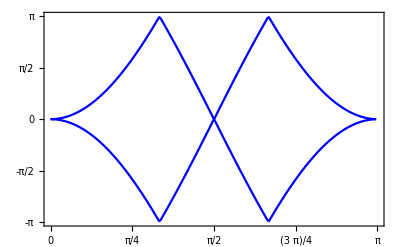

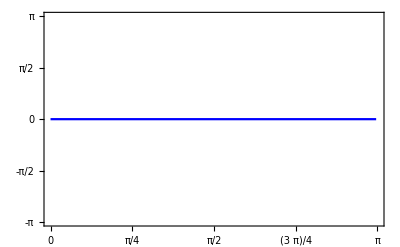

```mathematica
ClearAll["Global`*"];
$Assumptions={k∈ Reals,fi∈ Reals,theta∈ Reals,rho∈ Reals,nu∈ Reals,mu∈ Reals};


n3[a_,b_]:={
{Sin[a]*Cos[b]},
{Sin[a]*Sin[b]},
{Cos[a]}
};

H3[k_,fi_,theta_,nu_]:=k*(2*n3[theta,nu*fi].Transpose[n3[theta,nu*fi]]-DiagonalMatrix[{1,1,1}])


Print[Eigenvalues[H3[k,fi,theta,nu]]];

nu=1;
pts=250;

argsu=ConstantArray[0,{pts,2}];
argsv=ConstantArray[0,{pts,2}];

For[b=1,b<pts+1,b++,
theta=Pi*(b-1)/pts;
fi=0;

proju={{1,0},{0,1}};
projv=1;

eigs=Transpose[Sort[Transpose[Eigensystem[N[H3[1,fi,theta,nu]]]]]];
uS1=Normalize[eigs[[2,1]]];
uS2=Normalize[eigs[[2,2]]];
vS=Normalize[eigs[[2,3]]];

u1old=uS1;
u2old=uS2;
vold=vS;

For[a=1,a<pts+1,a++,
fi=2*a*Pi/pts;

eigs=Transpose[Sort[Transpose[Eigensystem[N[H3[1,fi,theta,nu]]]]]];
u1=Normalize[eigs[[2,1]]];
u2=Normalize[eigs[[2,2]]];
v=Normalize[eigs[[2,3]]];

Mu={{u1.Conjugate[u1old],u1.Conjugate[u2old]},{u2.Conjugate[u1old],u2.Conjugate[u2old]}};
Mv=v.Conjugate[vold];

proju=Mu.proju;
projv=Mv*projv;

u1old=u1;
u2old=u2;
vold=v;
];

proju={{uS1.Conjugate[u1old],uS1.Conjugate[u2old]},{uS2.Conjugate[u1old],uS2.Conjugate[u2old]}}.proju;
projv=(v.Conjugate[vold])*projv;

argsu[[b]]=Sort[Arg[Eigenvalues[proju]]];
argsv[[b]]=Arg[projv];
];

ListLinePlot[Transpose[argsu],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]

ListLinePlot[argsv,
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]
```

```mathematica
Exceptional  4-band models
```

{-1,-1,1,1}

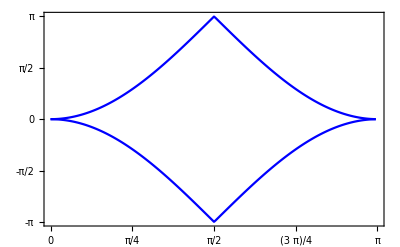

-Graphics-

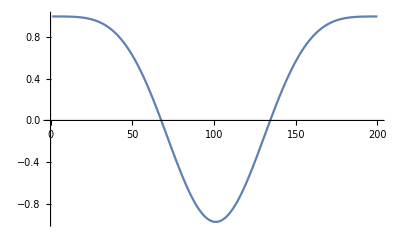

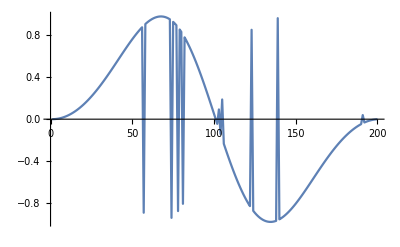

-Graphics-

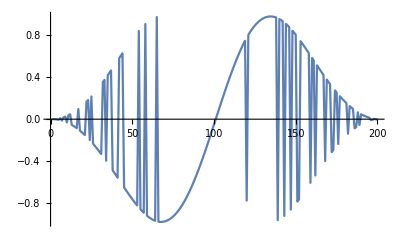

```mathematica
ClearAll["Global`*"];
$Assumptions={k∈ Reals,fi∈ Reals,theta∈ Reals,rho∈ Reals,nu∈ Reals,mu∈ Reals};


n4[a_,b_,c_]:={
{Cos[a]},
{Sin[a]*Cos[b]},
{Sin[a]*Sin[b]*Cos[c]},
{Sin[a]*Sin[b]*Sin[c]}
};
(*
H4[k_,fi_,theta_,nu_,mu_]:=k*(2*n4[0,0,0].Transpose[n4[0,0,0]]+2*n4[Pi/2,theta,nu*fi].Transpose[n4[Pi/2,theta,nu*fi]]-DiagonalMatrix[{1,1,1,1}])
*)

kx[fi_,theta_]:=Sin[theta]*Cos[fi];
ky[fi_,theta_]:=Sin[theta]*Sin[fi];
kz[fi_,theta_]:=Cos[theta];

(*
kx[fi_,theta_]:=(Sin[theta]*Cos[fi])^2-(Sin[theta]*Sin[fi])^2;
ky[fi_,theta_]:=2*Sin[theta]*Cos[fi]*Sin[theta]*Sin[fi];
kz[fi_,theta_]:=Cos[theta];

kx[fi_,theta_]:=(Sin[theta]*Cos[fi])^3-3*(Sin[theta]*Cos[fi])*(Sin[theta]*Sin[fi])^2;
ky[fi_,theta_]:=3*(Sin[theta]*Cos[fi])^2*(Sin[theta]*Sin[fi]) -(Sin[theta]*Sin[fi])^3;
kz[fi_,theta_]:=Cos[theta];
*)

H4[k_,f_,t_,nu_,mu_]:=k*{
{kz[f,t],0,kx[f,t],-ky[f,t]},
{0,kz[f,t],ky[f,t],kx[f,t]},
{kx[f,t],ky[f,t],-kz[f,t],0},
{-ky[f,t],kx[f,t],0,-kz[f,t]}
};

H4[k_,f_,t_,nu_,mu_]:=k*{
{kx[f,t],-ky[f,t],kz[f,t],0},
{-ky[f,t],-kx[f,t],0,kz[f,t]},
{kz[f,t],0,-kx[f,t],ky[f,t]},
{0,kz[f,t],ky[f,t],kx[f,t]}
};

Print[Sort[Eigenvalues[H4[1,fi,theta,nu,mu]]]];

nu=2;
mu=0;
pts=200;

argsu=ConstantArray[0,{pts,2}];
argsv=ConstantArray[0,{pts,2}];

uca=ConstantArray[0,{pts,1}];
usa=ConstantArray[0,{pts,1}];
vca=ConstantArray[0,{pts,1}];
vsa=ConstantArray[0,{pts,1}];


minishift=1/1000;
For[b=1,b<pts+1,b++,
theta=Max[Pi*(b-1)/pts-minishift,0];
fi=0;

proju={{1,0},{0,1}};
projv={{1,0},{0,1}};

eigs=Transpose[Sort[Transpose[Eigensystem[N[H4[1,fi,theta,nu,mu]]]]]];
uS1=Normalize[eigs[[2,1]]];
uS2=Normalize[eigs[[2,2]]];
vS1=Normalize[eigs[[2,3]]];
vS2=Normalize[eigs[[2,4]]];

u1old=uS1;
u2old=uS2;
v1old=vS1;
v2old=vS2;

For[a=1,a<pts+1,a++,
fi=2*a*Pi/pts;

eigs=Transpose[Sort[Transpose[Eigensystem[N[H4[1,fi,theta,nu,mu]]]]]];
u1=Normalize[eigs[[2,1]]];
u2=Normalize[eigs[[2,2]]];
v1=Normalize[eigs[[2,3]]];
v2=Normalize[eigs[[2,4]]];

Mu={{u1.Conjugate[u1old],u1.Conjugate[u2old]},{u2.Conjugate[u1old],u2.Conjugate[u2old]}};
Mv={{v1.Conjugate[v1old],v1.Conjugate[v2old]},{v2.Conjugate[v1old],v2.Conjugate[v2old]}};

proju=Mu.proju;
projv=Mv.projv;

u1old=u1;
u2old=u2;
v1old=v1;
v2old=v2;
];

proju={{uS1.Conjugate[u1old],uS1.Conjugate[u2old]},{uS2.Conjugate[u1old],uS2.Conjugate[u2old]}}.proju;
projv={{vS1.Conjugate[v1old],vS1.Conjugate[v2old]},{vS2.Conjugate[v1old],vS2.Conjugate[v2old]}}.projv;

uca[[b]]=proju[[1,1]];
usa[[b]]=proju[[1,2]];
vca[[b]]=projv[[1,1]];
vsa[[b]]=projv[[1,2]];

argsu[[b]]=Sort[Arg[Eigenvalues[proju]]];
argsv[[b]]=Sort[Arg[Eigenvalues[projv]]];
];

ListLinePlot[Transpose[argsu],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]

ListLinePlot[Transpose[argsv],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]

ListLinePlot[uca]
ListLinePlot[usa]
ListLinePlot[vca]
ListLinePlot[vsa]
```

```mathematica
Construct SrPtAs-like   TB model
```

```mathematica
ClearAll["Global`*"];
Needs["VectorAnalysis`"]
$Assumptions={kx∈ Reals,ky∈ Reals,kz∈ Reals,t1∈ Reals,t2∈ Reals,t3∈ Reals,m∈ Reals,t0};

one={{1,0},{0,1}};
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};

k={kx,ky,kz};

t[3]={1,0,0};
t[1]={-1/2,-Sqrt[3]/2,0};
t[2]={-1/2,+Sqrt[3]/2,0};

S0cost[kx_,ky_,kz_]:=Sum[Cos[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];
S0sint[kx_,ky_,kz_]:=Sum[Sin[DotProduct[{kx,ky,kz},t[n]]],{n,1,3}];

(*
H1[kx_,ky_,kz_,t1_]:=t1*(S0cost[kx,ky,kz]*KroneckerProduct[one,sx]-S0sint[kx,ky,kz]*KroneckerProduct[sz,sy]);
H2[kx_,ky_,kz_,t2_]:=2t2*Cos[kz]*KroneckerProduct[sx,sx];
H3[kx_,ky_,kz_,t0_,t3_,m_]:=(m+2t3*Cos[2kz])*KroneckerProduct[one,sz]+2t0*Cos[2kz]*KroneckerProduct[one,one];
*)

H1[kx_,ky_,kz_,t1_]:=t1*(S0cost[kx,ky,kz]*KroneckerProduct[one,sx]-S0sint[kx,ky,kz]*KroneckerProduct[one,sy]);
H2[kx_,ky_,kz_,t2_]:=2t2*Cos[kz]*KroneckerProduct[sx,one];
H3[kx_,ky_,kz_,t0_,t3_,m_]:=(m+2t3*Cos[2kz])*KroneckerProduct[sz,sz]+2t0*Cos[2kz]*KroneckerProduct[one,one];


H[kx_,ky_,kz_,t0_,t1_,t2_,t3_,m_]:=H1[kx,ky,kz,t1]+H2[kx,ky,kz,t2]+H3[kx,ky,kz,t0,t3,m];
```

```mathematica
Location of the nodal loops
```

```mathematica
Manipulate[Plot3D[Sort[Eigenvalues[N[H[kx,ky,kz,t0,t1,t2,t3,m]]]],{kx,-Pi,Pi},{ky,-Pi,Pi}],{kz,-Pi/2,Pi/2},{t0,-2,2},{t1,-2,2},{t2,-2,2},{t3,-2,2},{m,-2,2}]
```

```mathematica
FullSimplify[Eigenvalues[H[kx,ky,ArcCos[-m/2/t3]/2,0,t1,t2,t3,m]]]
```

{-√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])-2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])-2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),-√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))))}

```mathematica
{-√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])-2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])-2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),-√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))))}
```

{-√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])-2 Abs[t1] Abs[t2] √(t3 (-m+2 t3) (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])-2 Abs[t1] Abs[t2] √(t3 (-m+2 t3) (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),-√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+2 Abs[t1] Abs[t2] √(t3 (-m+2 t3) (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])))),√(1/t3(-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])+2 Abs[t1] Abs[t2] √(t3 (-m+2 t3) (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky]))))}

```mathematica
(* find condition on m for the central two states to have the same energy *)
FullSimplify[Solve[-t2^2 (m-2 t3)+t1^2 t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])==2 Abs[t1] Abs[t2] √(-(m-2 t3) t3 (3+4 Cos[(3 kx)/2] Cos[(√3 ky)/2]+2 Cos[√3 ky])),m]]
```

{{m→-(t3 (3 t1^2-2 t2^2+2 t1^2 (2 Cos[(3 kx)/2] Cos[(√3 ky)/2]+Cos[√3 ky])))/t2^2},{m→-(t3 (3 t1^2-2 t2^2+2 t1^2 (2 Cos[(3 kx)/2] Cos[(√3 ky)/2]+Cos[√3 ky])))/t2^2}}

```mathematica
(* compare to the expression in manuscript *)
FullSimplify[2t3*(1-(S0cost[kx,ky,kz]^2+S0sint[kx,ky,kz]^2)*(t1^2/(2*t2^2)))]
```

-(t3 (3 t1^2-2 t2^2+2 t1^2 (2 Cos[(3 kx)/2] Cos[(√3 ky)/2]+Cos[√3 ky])))/t2^2

```mathematica
Manipulate[DensityPlot[Log[((S0cost[kx,ky,kz]^2+S0sint[kx,ky,kz]^2)-2*(t2/t1)^2*(1-m/(2*t3)))^2],{kx,-Pi,Pi},{ky,-Pi,Pi},PlotPoints->100],{kz,-Pi/2,Pi/2},{t1,-2,2},{t2,-2,2},{t3,-2,2},{m,-2,2}]
```

```mathematica
Check Wilson loop spectra
```

```mathematica
t1=1;
t2=1.5;
t3=1;
t0=52.44; (* should not matter *)
m=0;

pts=51;

R=3/2;
xc=0;
yc=0;
zc= Pi/4; (* 0 or Pi/4 *)
 
argsu=ConstantArray[0,{pts+1,2}];
argsv=ConstantArray[0,{pts+1,2}];

For[b=1,b<pts+1,b++,
theta=Pi*(b-1)/pts;

fi=0;
kx=xc+R*Sin[theta]*Cos[fi];
ky=yc+R*Sin[theta]*Sin[fi];
kz=zc+R*Cos[theta];

proju={{1,0},{0,1}};
projv={{1,0},{0,1}};

eigs=Transpose[Sort[Transpose[Eigensystem[N[H[kx,ky,kz,t0,t1,t2,t3,m]]]]]];
uS1=Normalize[eigs[[2,1]]];
uS2=Normalize[eigs[[2,2]]];
vS1=Normalize[eigs[[2,3]]];
vS2=Normalize[eigs[[2,4]]];

u1old=uS1;
u2old=uS2;
v1old=vS1;
v2old=vS2;

For[a=1,a<pts+1,a++,
fi=2*a*Pi/pts;
kx=xc+R*Sin[theta]*Cos[fi];
ky=yc+R*Sin[theta]*Sin[fi];
kz=zc+R*Cos[theta];

eigs=Transpose[Sort[Transpose[Eigensystem[N[H[kx,ky,kz,t0,t1,t2,t3,m]]]]]];
u1=Normalize[eigs[[2,1]]];
u2=Normalize[eigs[[2,2]]];
v1=Normalize[eigs[[2,3]]];
v2=Normalize[eigs[[2,4]]];

Mu={{u1.Conjugate[u1old],u1.Conjugate[u2old]},{u2.Conjugate[u1old],u2.Conjugate[u2old]}};
Mv={{v1.Conjugate[v1old],v1.Conjugate[v2old]},{v2.Conjugate[v1old],v2.Conjugate[v2old]}};

proju=Mu.proju;
projv=Mv.projv;

u1old=u1;
u2old=u2;
v1old=v1;
v2old=v2;
];

proju={{uS1.Conjugate[u1old],uS1.Conjugate[u2old]},{uS2.Conjugate[u1old],uS2.Conjugate[u2old]}}.proju;
projv={{vS1.Conjugate[v1old],vS1.Conjugate[v2old]},{vS2.Conjugate[v1old],vS2.Conjugate[v2old]}}.projv;

argsu[[b]]=Sort[Arg[Eigenvalues[proju]]];
argsv[[b]]=Sort[Arg[Eigenvalues[projv]]];
];

ListLinePlot[Transpose[argsu],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]

ListLinePlot[Transpose[argsv],
PlotRange->{{1,pts+1},{-Pi,Pi}},
Frame-> True,
FrameTicks->{
{{1,0},{1+pts/4,Pi/4},{1+pts/2,Pi/2},{1+3*pts/4,3Pi/4},{1+pts,Pi}},
{-Pi,-Pi/2,0,Pi,Pi/2}
},
FrameTicksStyle->{{Directive[Thick,16],Directive[0]},{Directive[Thick,16],Directive[0]}},
PlotStyle->{Blue,Blue},
FrameStyle->Thick
]
```

Part::partw: Part 2 of Transpose[Transpose[Eigensystem[H[0.,0.,2.2854,52.44,1.,1.5,1.,0.]]]] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Plot the nodal loop trajectory
```

```mathematica
ClearAll["Global`*"];

plotpts=150;
thckns=0.008;
height=Pi/2;


m00=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67+4*0+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[-0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.5,0,0.5]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
m002=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67+4*0+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[-0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.5,0,0.5]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
n00=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67+4*0+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[-0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.5,0,0.5]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
n002=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67+4*0+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[-0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.5,0,0.5]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];


m10=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67+4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[-0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.75,0,0.25]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
m102=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67+4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[-0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.75,0,0.25]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
n10=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67+4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[-0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.75,0,0.25]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
n102=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67+4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[-0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.75,0,0.25]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];


m20=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67+4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[-1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[1,0,0]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
m202=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67+4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[-1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[1,0,0]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
n20=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67+4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[-1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[1,0,0]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
n202=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67+4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[-1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[1,0,0]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];


mm10=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.25,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
mm102=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.25,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
nm10=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.25,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
nm102=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*0.8+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[0.8/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.25,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];


mm20=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,1]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
mm202=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,1]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
nm20=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,1]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
nm202=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*1.6+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[1.6/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,1]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];


me0=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*2+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[2/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
me02=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*2+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[2/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
ne0=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*2+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[2/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
ne02=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*2+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[2/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0,0,0.75]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];


Lme0=ParametricPlot3D[{-2/3 (ArcCos[1/8 (3-4 Cos[√3 ky]) Sec[(√3 ky)/2]]),ky,ArcCos[0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.3,0.3,0.3]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
Lme02=ParametricPlot3D[{-2/3 (ArcCos[1/8 (3-4 Cos[√3 ky]) Sec[(√3 ky)/2]]),ky,-ArcCos[0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.3,0.3,0.3]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
Lne0=ParametricPlot3D[{2/3 (ArcCos[1/8 (3-4 Cos[√3 ky]) Sec[(√3 ky)/2]]),ky,ArcCos[0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.3,0.3,0.3]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];
Lne02=ParametricPlot3D[{2/3 (ArcCos[1/8 (3-4 Cos[√3 ky]) Sec[(√3 ky)/2]]),ky,-ArcCos[0/2]/2},{ky,-Pi,Pi},PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},PlotPoints-> plotpts,PlotStyle->Directive[Thickness[thckns],RGBColor[0.3,0.3,0.3]],RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False];


allSurface1=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*m+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[m/2]/2},{ky,-Pi,Pi},{m,-2,2},PlotPoints->30,PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False,PlotStyle-> Directive[RGBColor[0,1,0],Opacity[ 0.4]],MeshStyle->None];
allSurface2=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*m+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,ArcCos[m/2]/2},{ky,-Pi,Pi},{m,-2,2},PlotPoints->30,PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False,PlotStyle-> Directive[RGBColor[0,1,0],Opacity[ 0.4]],MeshStyle->None];
allSurface3=ParametricPlot3D[{-2/3 (ArcCos[-1/100 (67-4*m+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[m/2]/2},{ky,-Pi,Pi},{m,-2,2},PlotPoints->30,PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False,PlotStyle-> Directive[RGBColor[0,1,0],Opacity[ 0.4]],MeshStyle->None];
allSurface4=ParametricPlot3D[{2/3 (ArcCos[-1/100 (67-4*m+50 Cos[√3 ky]) Sec[(√3 ky)/2]]-2 π *0),ky,-ArcCos[m/2]/2},{ky,-Pi,Pi},{m,-2,2},PlotPoints->30,PlotRange->{{-Pi,Pi},{-Pi,Pi},{-height,height}},RegionFunction->Function[{x,y,z},Abs[x]<2*Pi/3&&Abs[x+y*Sqrt[3]]<4*Pi/3&&Abs[x-y*Sqrt[3]]<4*Pi/3],Boxed->False,Axes->False,PlotStyle-> Directive[RGBColor[0,1,0],Opacity[ 0.4]],MeshStyle->None];


Lv1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-height},{0,4*Pi/3/Sqrt[3],+height}}]];
Lv2=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-height},{0,-4*Pi/3/Sqrt[3],+height}}]];
Lv3=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-height},{2*Pi/3,2*Pi/3/Sqrt[3],+height}}]];
Lv4=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-height},{2*Pi/3,-2*Pi/3/Sqrt[3],+height}}]];
Lv5=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-height},{-2*Pi/3,2*Pi/3/Sqrt[3],+height}}]];
Lv6=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-height},{-2*Pi/3,-2*Pi/3/Sqrt[3],+height}}]];

Ltop1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],+height},{2*Pi/3,2*Pi/3/Sqrt[3],+height}}]];
Ltop2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],+height},{2*Pi/3,-2*Pi/3/Sqrt[3],+height}}]];
Ltop3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],+height},{0,-4*Pi/3/Sqrt[3],+height}}]];
Ltop4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],+height},{-2*Pi/3,-2*Pi/3/Sqrt[3],+height}}]];
Ltop5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],+height},{-2*Pi/3,2*Pi/3/Sqrt[3],+height}}]];
Ltop6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],+height},{0,4*Pi/3/Sqrt[3],+height}}]];

Lbot1=Graphics3D[Line[{{0,4*Pi/3/Sqrt[3],-height},{2*Pi/3,2*Pi/3/Sqrt[3],-height}}]];
Lbot2=Graphics3D[Line[{{2*Pi/3,2*Pi/3/Sqrt[3],-height},{2*Pi/3,-2*Pi/3/Sqrt[3],-height}}]];
Lbot3=Graphics3D[Line[{{2*Pi/3,-2*Pi/3/Sqrt[3],-height},{0,-4*Pi/3/Sqrt[3],-height}}]];
Lbot4=Graphics3D[Line[{{0,-4*Pi/3/Sqrt[3],-height},{-2*Pi/3,-2*Pi/3/Sqrt[3],-height}}]];
Lbot5=Graphics3D[Line[{{-2*Pi/3,-2*Pi/3/Sqrt[3],-height},{-2*Pi/3,2*Pi/3/Sqrt[3],-height}}]];
Lbot6=Graphics3D[Line[{{-2*Pi/3,2*Pi/3/Sqrt[3],-height},{0,4*Pi/3/Sqrt[3],-height}}]];

Rasterize[Show[{m00,m002,n00,n002,m10,m102,n10,n102,m20,m202,n20,n202,mm10,mm102,nm10,nm102,mm20,mm202,nm20,nm202,me0,me02,ne0,ne02,Lme0,Lme02,Lne0,Lne02,Lv1,Lv2,Lv3,Lv4,Lv5,Lv6,Ltop1,Ltop2,Ltop3,Ltop4,Ltop5,Ltop6,Lbot1,Lbot2,Lbot3,Lbot4,Lbot5,Lbot6,allSurface1,allSurface2,allSurface3,allSurface4},ViewPoint->{2,2,1},BoxRatios->{1,1,1}],RasterSize->1000]
```

-Graphics-